```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwhm="/home/simonfreedman/Code/cytomod/shila/semiflexible/out/pl/";
```

```mathematica
U[θ_,βκover2L_,a_]:=βκover2L*(θ+a)^2;
P[A_,βκover2L_,θ_,a_]:=A Exp[-U[θ,βκover2L,a]];
```

```mathematica
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
(*Print["Finished importing "<>file];*)
timestamps = Position[particles,"t"][[All,1]];
particlesT=Table[particles[[timestamps[[i]]+1;;timestamps[[i+1]]-1]],{i,Length[timestamps]-1}];
particlesT=Append[particlesT, particles[[timestamps[[-1]]+1;;]]];
nparticles=Length[particlesT[[1]]];
dt=particles[[timestamps[[2]],3]]-particles[[timestamps[[1]],3]];
{nparticles, dt,particlesT}
];
```

```mathematica
AngleDistribution[d_,decorframe_]:=
Module[
{dir =d,
ndc=decorframe},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
{np,dt,lt}=ParticleTimeSeries[d,"links"];
nlinksT=Table[Length[l],{l,lt}];
fracture=Position[nlinksT,Except[Head[nlinksT]|nlinksT[[1]]],1,1];
fractureT=If[Length[fracture]>0, fracture[[1,1]],Length[rt]];
rt=rt[[1;;fractureT]];
ld=Sqrt[Total[rt[[1,1,3;;4]]^2]];
(*anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];*)
angleDiffs=Table[ArcCos[rt[[t,i+1,3;;4]].rt[[t,i,3;;4]]/ld^2],{t,1,Length[rt]},{i,1,Length[rt[[t]]]-1}];
bins=BinCounts[Flatten[angleDiffs],{0,Pi,.1}];
bins
];
```

```mathematica
AngleDistribution[d_,decorframe_]:=
Module[
{dir =d,
ndc=decorframe},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
{np,dt,lt}=ParticleTimeSeries[d,"links"];
nlinksT=Table[Length[l],{l,lt}];
fracture=Position[nlinksT,Except[Head[nlinksT]|nlinksT[[1]]],1,1];
fractureT=If[Length[fracture]>0, fracture[[1,1]],Length[rt]];
rt=rt[[1;;fractureT]];
ld=Sqrt[Total[rt[[1,1,3;;4]]^2]];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
angleDiffs=Table[anglesT[[t,i+1]]-anglesT[[t,i]],{t,1,Length[rt]},{i,1,Length[rt[[t]]]-1}];
bins=BinCounts[Flatten[angleDiffs],{-Pi,Pi,.01}];
bins
];
```

```mathematica
nmons=Table[ToString[i],{i,2,48}];
basedir="kbp04_nm";
dirs=Table[mdwlcl<>basedir<>s,{s,nmons}];
```

```mathematica
dists=Table[AngleDistribution[d,1],{d,dirs}];
```

```mathematica
angs=Table[i,{i,-Pi+.05,Pi-.05,.01}];
dats=Table[{angs[[i]],dists[[j,i]]},{j,1,Length[dists]},{i,1,Length[angs]}];
```

```mathematica
nlms=Table[
NonlinearModelFit[
dats[[i]],
P[A,βκover2L,θ,a],
{{A,Max[dats[[i,All,2]]]},{βκover2L,(1/.004)*0.04/(2*0.8)},{a,0}},
θ],
{i,Length[dats]}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

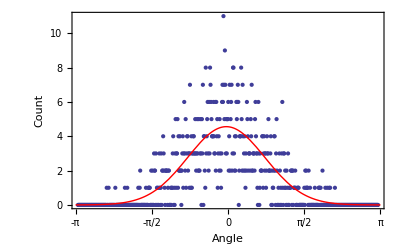
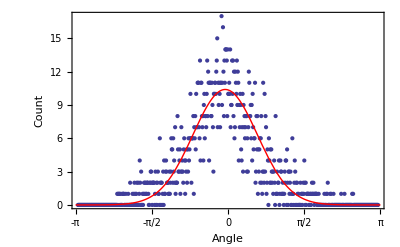
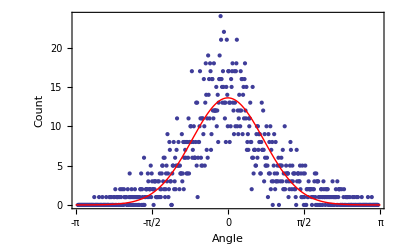
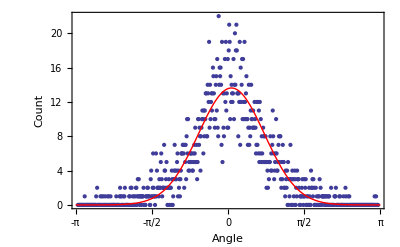
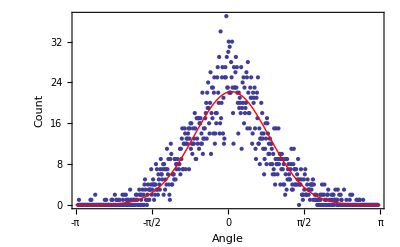
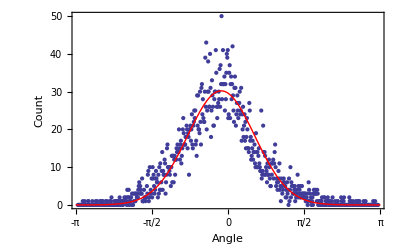
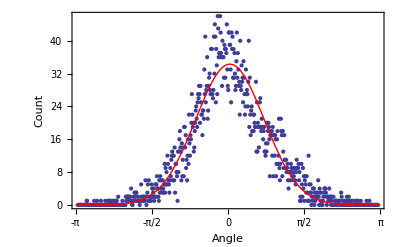
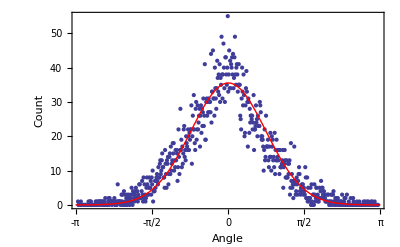

```mathematica
Table[Show[ListPlot[dists[[i]],DataRange->{-Pi+.05,Pi-0.05},PlotRange->Full, Frame->True, FrameLabel->{"Angle", "Count","nmon = "<>nmons[[i]]},Ticks->{Range[-Pi,Pi,Pi/8],Automatic}]
,Plot[Normal[nlms[[i]]]/.θ->x,{x,-Pi,Pi},PlotRange->Full,PlotStyle->{Red,Thick}]
]
,{i,Length[dists]}]
```

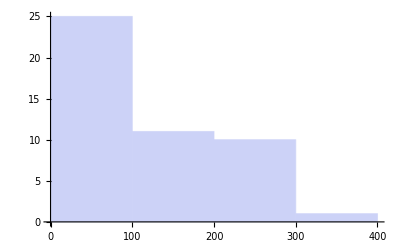
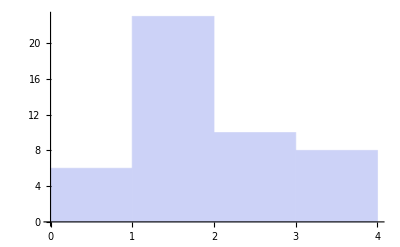
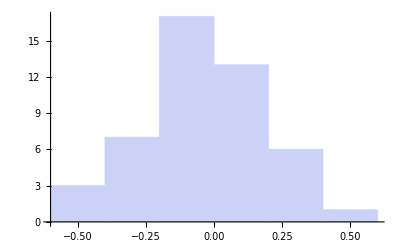

```mathematica
Table[Histogram[Table[nlms[[i]]["ParameterTableEntries"][[j,1]],{i,Length[nlms]}]],{j,1,3}]
```

```mathematica
allCoeffs=Table[nlms[[i]]["ParameterTableEntries"][[2,1]],{i,Length[nlms]}];
offsets=Table[nlms[[i]]["ParameterTableEntries"][[3,1]],{i,Length[nlms]}];
```

```mathematica
Mean[allCoeffs]
```

1.85924

```mathematica
Mean[offsets]
```

-0.0350311

```mathematica
myβκover2L=.04/.004/2/0.8
```

6.25

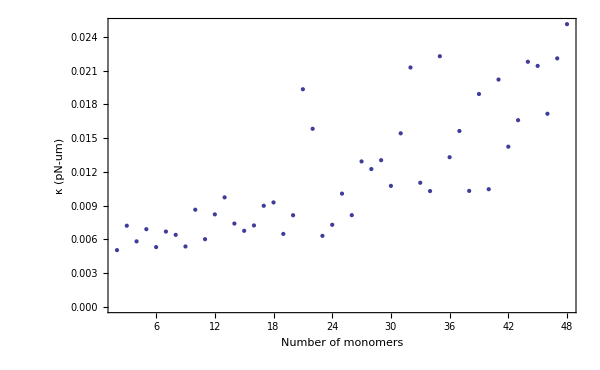

```mathematica
Show[ListPlot[allCoeffs*0.8*2*.004, DataRange->{2,48},PlotRange->Full],Plot[1,{x,2,48}],Frame->True, FrameLabel->{"Number of monomers", "κ (pN-um)","Bending modulus κ Extracted from Model"},BaseStyle->{FontSize->16}]
```